```mathematica
Get["DMTestFunctions`"]
Get["DifferenceMapOptimizer`"]
Get["DMData`"]
Get["DMUtils`"]
```

```mathematica
builtinMethods = {"SimulatedAnnealing", "DifferentialEvolution", "NelderMead", "RandomSearch"};
vars = {x, y};
nicePlotBad[method_] := Module[{fun, solution, minima, offset, range},
offset = {100, 100};
range = Sequence[{x, -10, 10}, {y, -10, 10}];
{{fun, solution}, {minima}} =
Reap[
NMinimize[
griewankN[vars - offset],
{x, y}, 
EvaluationMonitor-> Hold[Sow[vars]], 
Method->method, 
MaxIterations->100]
];
Show[
ContourPlot[griewankN[vars - offset], Evaluate[range], PlotPoints -> 45, ColorFunction -> "CherryTones"], ListPlot[minima, Joined->True], 
ListPlot[{Map[# /. solution &, vars]}]
]
];
nicePlotGood[method_] := Module[{fun, solution, minima, offset, range},
offset = {100, 100};
range = Sequence[{x, 0, 200}, {y, 0, 200}];
{{fun, solution}, {minima}} =
Reap[
NMinimize[
griewankN[vars - offset],
{{x, -500.0, 500.0}, {y, -500.0, 500.0}}, 
EvaluationMonitor-> Hold[Sow[vars]], 
Method->method, 
MaxIterations->100]
];
Show[
ContourPlot[griewankN[vars - offset], Evaluate[range], PlotPoints -> 45, ColorFunction -> "CherryTones"], ListPlot[minima, Joined->True], 
ListPlot[{Map[# /. solution &, vars]}]
]
];
Map[{Map[#, builtinMethods], builtinMethods} &, {nicePlotBad, nicePlotGood}]
it = %;
Grid[Map[{Grid[#]} &, it]]
Export["mma-compare-brackets.pdf", %]
```

```mathematica
vars = {x, y};
offset = {100, 100};
range = Sequence[{x, 0, 200}, {y, 0, 200}];
Module[{fun, solution, minima},
minima = DifferenceMapOptimizer[
griewankN[vars - offset],
{x, y}, 
35,
10^-4,
verbosity -> 2,
startpoint -> {{50, 50}, {42, 43}}][["minima"]] // Map[#[[2]] &];
Show[
ContourPlot[griewankN[vars - offset], Evaluate[range], PlotPoints -> 45, ColorFunction -> "CherryTones"], ListPlot[minima, Joined->True]
]
]
```

-Graphics-

```mathematica
(* Create a plot of the griewank function with the three initial points (x_0, x_0^*, and x_1) overlayed (hard to see.) *)
start = {4, 7};
other = {7, 8};
fun = N[griewankN[start]];
{fun2, solution} = FindMinimum[griewankN[{x, y}], {x, 4}, {y, 7}];
sol = {x, y} /. solution
Show[Plot3D[griewankN[{x, y}], {x, -10, 10}, {y, -10, 10}], ListPointPlot3D[{Join[start, {fun+0.01}],  Join[sol, {fun2+0.02}], Append[other, griewankN[other]]}]]
```

{3.14002,4.43844}

```mathematica
Plus @@ <|
"d" -> 1,
"e" -> 5
|>
```

6

```mathematica
(* EXPERIMENT *)
With[{
dim = 4,
maxnfev = 20000,
innerNiter = 65,
secondPointDistance = 5,
prelimRunCount = 10,
prelimNiter = 5
},
Module[{preliminaryResults, itersPerSolver},
(* Collect preliminary results to estimate how many function evaluations are needed per iteration for each solver. With this information, we can then estimate how many iterations to run each solver for, on top of using a random restart strategy (implemented in DMData.m). *)
preliminaryResults = ToAssociations[
makeResults[
<|
"dim" -> dim,
"niter" -> prelimNiter,
"runCount" -> prelimRunCount,
"innerNiter" -> innerNiter,
"secondPointDistance" -> secondPointDistance,
"tolerance" -> 1 10^-8,
"randomrestart" -> False,
"maxnfev" -> 1,
"solversToDo" -> {"sa", "de", "nm", "rs", "dm"} (* all the solvers *)
|>
]
];
Print["Determining number of iterations for 20000 function evaluations."];
itersPerSolver = maxnfev / (Map[
Function[solverData,
N @* Plus @@ Map[
Function[functionData,
Plus @@ Map[#[["nfev"]] &, functionData] / prelimRunCount (* average over runs *)
],
solverData
] / Length[solverData] (* average over number of objective functions *)
],
preliminaryResults
] / prelimNiter); (* nfevs per iteration *)
Print[itersPerSolver];
]
]
```

### Solver: dm

### Solver: de

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 5 iterations.

General::stop: Further output of NMinimize :: cvmit will be suppressed during this calculation.

### Solver: sa

### Solver: nm

### Solver: rs

Determining number of iterations for 20000 function evaluations.

<|dm→71.9135,de→213.493,sa→337.154,nm→426.985,rs→10.6867|>

```mathematica
builtinResults = ToAssociations[
makeResults[
<|
"dim" -> 4,
"niter" -> 100,
"runCount" -> 10,
"innerNiter" -> 65,
"secondPointDistance" -> 5,
"maxnfev" -> 14000,
"solversToDo" -> {"sa", "de", "nm", "rs"}
|>
]
];
```

```mathematica
builtinResults[["sa", "griewank", 1, "fun"]]
```

0.184822

```mathematica
builtinResults
```

<|sa→<|griewank→{1},3,ackley→{<|fun→15.3004,x→{-4.99394,3},nfev→1,iterate→{{19.2651,22.0438,11.0937,29.9648},{2.67236,-2.0398,29.936,-3.88149},90,{-4.99394,-3.99515,-4.74188×10^-9,12.9842}}|>,<|1|>,<|1|>}|>|>
 |  |  |  |

{{{56.5,0.799247}},{{61.5,1.70889}},{{62.8,0.986467}},{{34.5,2.29591}}}

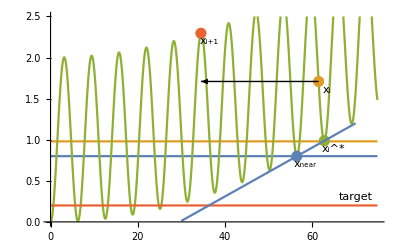

```mathematica
below[{x_, y_}] := {x + 2, y - 0.1};
xs = {56.5, 61.5, 62.8, 34.5};
pts = Map[{{#, griewankN @ {#}}} &, xs]
g = Show[
Plot[{0.8, 0.98, griewankN @ {xi}, 0.2}, {xi, 0, 75}, PlotRange -> {0, 2.5}],
ListPlot[pts],
With[{a = (pts[[3]][[1]][[2]] - pts[[1]][[1]][[2]]) / (pts[[3]][[1]][[1]] - pts[[1]][[1]][[1]])},
With[{b = pts[[1]][[1]][[2]] - a * pts[[1]][[1]][[1]]},
Plot[a * x + b, {x, 30, 70}]
]
],
Graphics[Arrow[{pts[[2]][[1]],pts[[2]][[1]] + {-27, 0}}]],
Graphics[Text[Subscript[x, i], below[pts[[2]][[1]]]]],
Graphics[Text[Subscript[x, near], below[pts[[1]][[1]]]]],
Graphics[Text[Subscript[x, i + 1], below[pts[[4]][[1]]]]],
Graphics[Text[Subsuperscript[x, i, "*"], below[pts[[3]][[1]]]]],
Graphics[Text["target", {70, 0.3}]]
]
Export["iterating-base.pdf", g];
```